```mathematica
(*THIS MATH AND PHYSICS NEEDS SOME RIGID BODY PHYSICS PROBABLY*)
ClearAll["Global`*"]
x1[t_] :=r1*-Sin[a1[t]];
y1[t_]:=r1*Cos[a1[t]];
x2[t_] := r1*-Sin[a1[t]]+r2*-Sin[a1[t]+a2[t]];
y2[t_] := r1*Cos[a1[t]]+r2*Cos[a1[t]+a2[t]];
x3[t_] := r1*-Sin[a1[t]]+r2*-Sin[a1[t]+a2[t]]+r3*-Sin[a1[t]+a2[t]+a3[t]];
y3[t_] := r1*Cos[a1[t]]+r2*Cos[a1[t]+a2[t]]+r3*Cos[a1[t]+a2[t]+a3[t]];
```

```mathematica
T = Simplify[TrigReduce[1/2*(m1(x1'[t]^2+y1'[t]^2)+m2(x2'[t]^2+y2'[t]^2)+m3(x3'[t]^2+y3'[t]^2))]]
```

1/2 ((m1 r1^2+m2 r1^2+m3 r1^2+m2 r2^2+m3 r2^2+m3 r3^2+2 (m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+2 m3 r1 r3 Cos[a2[t]+a3[t]]) a1'[t]^2+(m2 r2^2+m3 (r2^2+r3^2)+2 m3 r2 r3 Cos[a3[t]]) a2'[t]^2+2 m3 r3 (r3+r2 Cos[a3[t]]) a2'[t] a3'[t]+m3 r3^2 a3'[t]^2+2 a1'[t] ((m2 r2^2+m3 r2^2+m3 r3^2+(m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+m3 r1 r3 Cos[a2[t]+a3[t]]) a2'[t]+m3 r3 (r3+r2 Cos[a3[t]]+r1 Cos[a2[t]+a3[t]]) a3'[t]))

```mathematica
k = {k1, k2, k3, k4, k5, k6};
ra = {ra1, ra2, ra3};
friction = {fr1, fr2, fr3};
Lang = {{d11, d12, d13},{d21, d22,d23},{d31,d32,d33}, {d41,d42,d43},{d51, d52, d53}, {d61, d62, d63}};
initDef = {def1, def2, def3, def4, def5, def6};
```

```mathematica
V = 1/2*(k[[1]]*(Lang[[1,1]]*a1[t]*ra[[1]]+Lang[[1,2]]*(a2[t])*ra[[2]]+Lang[[1,3]]*(a3[t])*ra[[3]]+initDef[[1]])^2+
k[[2]]*(Lang[[2,1]]*a1[t]*ra[[1]]+Lang[[2,2]]*(a2[t])*ra[[2]]+Lang[[2,3]]*(a3[t])*ra[[3]]+initDef[[2]])^2+
k[[3]]*(Lang[[3,1]]*a1[t]*ra[[1]]+Lang[[3,2]]*(a2[t])*ra[[2]]+Lang[[3,3]]*(a3[t])*ra[[3]]+initDef[[3]])^2+ 
k[[4]]*(Lang[[4,1]]*a1[t]*ra[[1]]+Lang[[4,2]]*(a2[t])*ra[[2]]+Lang[[4,3]]*(a3[t])*ra[[3]]+initDef[[4]])^2+k[[5]]*(Lang[[5,1]]*a1[t]*ra[[1]]+Lang[[5,2]]*(a2[t])*ra[[2]]+Lang[[5,3]]*(a3[t])*ra[[3]]+initDef[[5]])^2+k[[6]]*(Lang[[6,1]]*a1[t]*ra[[1]]+Lang[[6,2]]*(a2[t])*ra[[2]]+Lang[[6,3]]*(a3[t])*ra[[3]]+initDef[[6]])^2)
```

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t]+d13 ra3 a3[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t]+d23 ra3 a3[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t]+d33 ra3 a3[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]+d43 ra3 a3[t])^2+k5 (def5+d51 ra1 a1[t]+d52 ra2 a2[t]+d53 ra3 a3[t])^2+k6 (def6+d61 ra1 a1[t]+d62 ra2 a2[t]+d63 ra3 a3[t])^2)

```mathematica
Fr =  1/2*(friction[[1]]*a1'[t]^2+friction[[2]]*a2'[t]^2+friction[[3]]*a3'[t]^2 )
```

1/2 (fr1 a1'[t]^2+fr2 a2'[t]^2+fr3 a3'[t]^2)

```mathematica
L = T-V
H = T+V
TotEng = T+V+Fr
```

1/2 (-k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t]+d13 ra3 a3[t])^2-k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t]+d23 ra3 a3[t])^2-k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t]+d33 ra3 a3[t])^2-k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]+d43 ra3 a3[t])^2-k5 (def5+d51 ra1 a1[t]+d52 ra2 a2[t]+d53 ra3 a3[t])^2-k6 (def6+d61 ra1 a1[t]+d62 ra2 a2[t]+d63 ra3 a3[t])^2)+1/2 ((m1 r1^2+m2 r1^2+m3 r1^2+m2 r2^2+m3 r2^2+m3 r3^2+2 (m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+2 m3 r1 r3 Cos[a2[t]+a3[t]]) a1'[t]^2+(m2 r2^2+m3 (r2^2+r3^2)+2 m3 r2 r3 Cos[a3[t]]) a2'[t]^2+2 m3 r3 (r3+r2 Cos[a3[t]]) a2'[t] a3'[t]+m3 r3^2 a3'[t]^2+2 a1'[t] ((m2 r2^2+m3 r2^2+m3 r3^2+(m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+m3 r1 r3 Cos[a2[t]+a3[t]]) a2'[t]+m3 r3 (r3+r2 Cos[a3[t]]+r1 Cos[a2[t]+a3[t]]) a3'[t]))

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t]+d13 ra3 a3[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t]+d23 ra3 a3[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t]+d33 ra3 a3[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]+d43 ra3 a3[t])^2+k5 (def5+d51 ra1 a1[t]+d52 ra2 a2[t]+d53 ra3 a3[t])^2+k6 (def6+d61 ra1 a1[t]+d62 ra2 a2[t]+d63 ra3 a3[t])^2)+1/2 ((m1 r1^2+m2 r1^2+m3 r1^2+m2 r2^2+m3 r2^2+m3 r3^2+2 (m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+2 m3 r1 r3 Cos[a2[t]+a3[t]]) a1'[t]^2+(m2 r2^2+m3 (r2^2+r3^2)+2 m3 r2 r3 Cos[a3[t]]) a2'[t]^2+2 m3 r3 (r3+r2 Cos[a3[t]]) a2'[t] a3'[t]+m3 r3^2 a3'[t]^2+2 a1'[t] ((m2 r2^2+m3 r2^2+m3 r3^2+(m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+m3 r1 r3 Cos[a2[t]+a3[t]]) a2'[t]+m3 r3 (r3+r2 Cos[a3[t]]+r1 Cos[a2[t]+a3[t]]) a3'[t]))

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t]+d13 ra3 a3[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t]+d23 ra3 a3[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t]+d33 ra3 a3[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]+d43 ra3 a3[t])^2+k5 (def5+d51 ra1 a1[t]+d52 ra2 a2[t]+d53 ra3 a3[t])^2+k6 (def6+d61 ra1 a1[t]+d62 ra2 a2[t]+d63 ra3 a3[t])^2)+1/2 (fr1 a1'[t]^2+fr2 a2'[t]^2+fr3 a3'[t]^2)+1/2 ((m1 r1^2+m2 r1^2+m3 r1^2+m2 r2^2+m3 r2^2+m3 r3^2+2 (m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+2 m3 r1 r3 Cos[a2[t]+a3[t]]) a1'[t]^2+(m2 r2^2+m3 (r2^2+r3^2)+2 m3 r2 r3 Cos[a3[t]]) a2'[t]^2+2 m3 r3 (r3+r2 Cos[a3[t]]) a2'[t] a3'[t]+m3 r3^2 a3'[t]^2+2 a1'[t] ((m2 r2^2+m3 r2^2+m3 r3^2+(m2+m3) r1 r2 Cos[a2[t]]+2 m3 r2 r3 Cos[a3[t]]+m3 r1 r3 Cos[a2[t]+a3[t]]) a2'[t]+m3 r3 (r3+r2 Cos[a3[t]]+r1 Cos[a2[t]+a3[t]]) a3'[t]))

```mathematica
a1Solve = D[D[L,a1'[t]],t]==D[L,a1[t]]-D[Fr,a1'[t]];
a2Solve = D[D[L,a2'[t]],t]==D[L,a2[t]]-D[Fr,a2'[t]];
a3Solve = D[D[L,a3'[t]],t]==D[L,a3[t]]-D[Fr,a3'[t]];
```

```mathematica
sol = Solve[{a1Solve, a2Solve,a3Solve}, {a1''[t], a2''[t],a3''[t]}][[1]];
(*a2sol = Simplify[TrigReduce[Solve[a2Solve, a2''[t]][[1]]]]*)
```

```mathematica
(*THIS SYSTEM ASSUMES MASS IS AT TIP OF FINGER OBJECT*)
```

```mathematica
parameters = {
m1->1,
m2->1,
m3->1,

r1->1/20, 
r2->1/20,
r3->1/20,

k1->100,
k2->100,
k3->100,
k4->100,
k5->100,
k6->100,

fr1->1/50,
fr2->1/50,
fr3->1/50,

ra1->1/50,
ra2->1/50,
ra3->1/50,

d11->-1, d12->-1,d13->-1,
d21->1, d22->1,d23->1,
d31->-1, d32->-1,d33->1,
d41->1, d42->1,d43->-1,
d51->-1, d52->1,d53->1,
d61->1, d62->-1,d63->-1,
(*-1 means clockwise, 1 means counter clockwise, 0 means no effect*)

def1->.05,
def2->.1,
def3->.05,
def4->.1,
def5->.1,
def6->.05};
soltime = 30;
```

```mathematica
goveq1 = a1''[t]==(a1''[t]/.sol)/.parameters;
goveq2 = a2''[t] ==(a2''[t] /.sol)/.parameters;
goveq3 = a3''[t] ==(a3''[t] /.sol)/.parameters;
(*NOTE: Don't use this --> Method->{"EquationSimplification"->"Residual"};
It is restrictive whereas not setting it uses multiple methods for simplification.*)
(*s = NDSolve[{governingEq1,a1[0]==0, a1'[0]== 0},a1[t],{t,0,soltime}]*)
s = NDSolve[{
goveq1,a1[0]==.01, a1'[0]== 0,
goveq2,a2[0]==.01, a2'[0]==0,
goveq3,a3[0]==.01, a3'[0]==0},
{a1[t],a2[t],a3[t]},{t,0,soltime}];
finsol = {
s[[1,1]],s[[1,2]],s[[1,3]],
D[s,t][[1,1]],D[s,t][[1,2]],D[s,t][[1,3]],
D[s,{t,2}][[1,1]], D[s,{t,2}][[1,2]],D[s,{t,2}][[1,3]]
};
(*s2 =  NDSolve[{governingEq1, governingEq2,a1[0]==0, a1'[0]== 0, a2[0]==0, a2'[0]==0},a2[t],{t,0,soltime} ,Method->{"EquationSimplification"->"Residual"}]*)
```

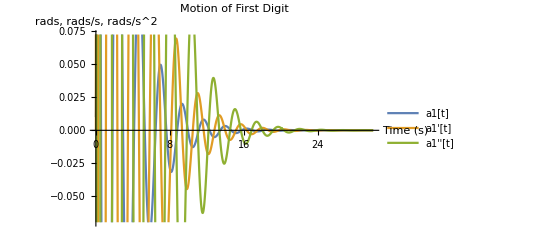

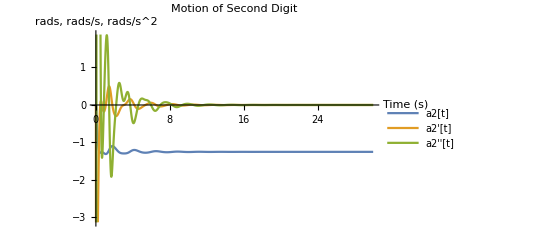

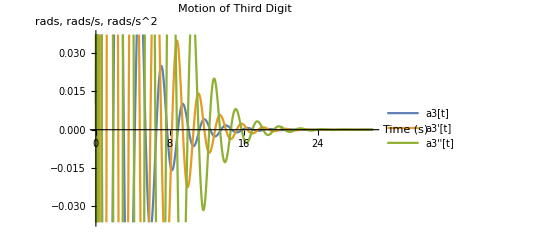

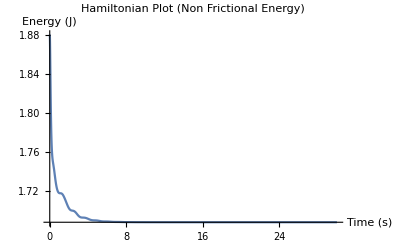

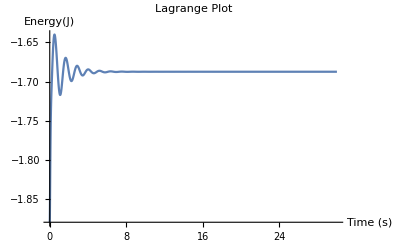

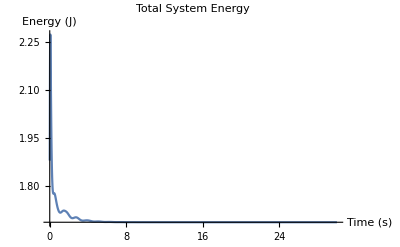

```mathematica
Plot[{a1[t]/.finsol, a1'[t]/.finsol, a1''[t]/.finsol},{t,0,soltime},PlotLabel->"Motion of First Digit", PlotLegends->{"a1[t]", "a1'[t]", "a1''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
Plot[{a2[t]/.finsol, a2'[t]/.finsol, a2''[t]/.finsol},{t,0,soltime},PlotLabel->"Motion of Second Digit", PlotLegends->{"a2[t]", "a2'[t]", "a2''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
Plot[{a3[t]/.finsol, a3'[t]/.finsol, a3''[t]/.finsol},{t,0,soltime},PlotLabel->"Motion of Third Digit", PlotLegends->{"a3[t]", "a3'[t]", "a3''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
Plot[Evaluate[H/.parameters/.finsol],{t,0,soltime},PlotLabel->"Hamiltonian Plot (Non Frictional Energy)",AxesLabel->{"Time (s)","Energy (J)"},PlotRange->Full]
Plot[Evaluate[L/.parameters/.finsol],{t,0,soltime},PlotLabel->"Lagrange Plot",AxesLabel->{"Time (s)","Energy(J)"}, PlotRange->Full]
Plot[Evaluate[TotEng/.parameters/.finsol],{t,0,soltime},PlotLabel->"Total System Energy",AxesLabel->{"Time (s)","Energy (J)"}, PlotRange->Full]
```

```mathematica
(*ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s[[1]]],{t,0,soltime},PlotRange->{{-.15,.15},{-.15,.15}},AxesLabel-> {"î","ĵ"}]
ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s[[1]]],{t,0,soltime},PlotRange->{{-.15,.15},{-.15,.15}},AxesLabel-> {"î","ĵ"}]*)
```

```mathematica
(*{{0,0},{x1[t],1},{2,2}}/.parameters/.finsol/.{t->t0}*)
```

```mathematica
tailLen = .2;
Animate[Show[{
(*First End Effector (Second Joint)*)
ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s],{t,0,t0},AxesOrigin->{0,0},PlotRange->{{-.2,.2},{-.2, .2}},AspectRatio->1,ImageSize->500, PlotStyle->{Blue},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s],{t,Max[t0-tailLen,0],t0}, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}],

(*Second End Effector (Third Joint)*)
ParametricPlot[Evaluate[{x2[t],y2[t]}/.parameters/.s],{t,0,t0},PlotStyle->{Orange},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x2[t],y2[t]}/.parameters/.s],{t,Max[t0-tailLen,0],t0}, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}],

(*Third End Effector (Fingertip Joint)*)
ParametricPlot[Evaluate[{x3[t],y3[t]}/.parameters/.s],{t,0,t0}, PlotStyle->{Magenta},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x3[t],y3[t]}/.parameters/.s],{t,Max[t0-tailLen,0],t0}, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}],

(*Bones*)
Graphics[{Thick, Line[Evaluate[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}}/.parameters/.finsol/.{t->t0}]]}]
}],{t0, 0 ,soltime}, AnimationRate->1]
```